## Shared Helpers

```mathematica
(* ================================================================== *)
(* Figure 13 Replication: Suppress + Inject Position Sweep            *)
(* candle-mi example: figure13_planning_poems                         *)
(* ================================================================== *)

(* Shared helper: extract sweep data from a JSON association *)
extractSweep[d_] := Module[{sw = d["sweep"]},
  <|
    "positions" -> sw[[All, "position"]],
    "probs"     -> sw[[All, "prob"]],
    "tokens"    -> sw[[All, "token"]],
    "baseline"  -> d["baseline_prob"]
  |>]
```

```mathematica
(* Shared helper: clean token labels for display *)
cleanToken[t_] := StringReplace[t, {
  "\n" -> "\\n",
  " " -> " "}]
```

```mathematica
(* Shared helper: build styled bar data (first=dark gray, last=red, rest=gray) *)
styledBars[allProbs_, nAll_] := MapIndexed[
  Style[#1, Which[
    First[#2] == 1, GrayLevel[0.4],
    First[#2] == nAll, Darker[Red],
    True, GrayLevel[0.6]
  ]] &,
  allProbs]
```

## Llama 3.2 1B with 524K CLTs

```mathematica
(* Figure 13 Replication: Suppress + Inject Position Sweep *)
(* Llama 3.2 1B with 524K CLT *)
(* Import JSON output from candle-mi figure13_planning_poems example *)

llamaData = Import[
  FileNameJoin[{NotebookDirectory[], "llama_output.json"}],
  "RawJSON"
];

llamaSweep = extractSweep[llamaData];
llamaProbs = llamaSweep["probs"];
llamaTokens = llamaSweep["tokens"];
llamaBaseline = llamaSweep["baseline"];
llamaLabels = cleanToken /@ llamaTokens;

(* Prepend baseline as "No Steering" bar *)
llamaAllProbs = Prepend[llamaProbs, llamaBaseline];
llamaAllLabels = Prepend[llamaLabels, "No Steering"];
nLlama = Length[llamaAllProbs]
```

32

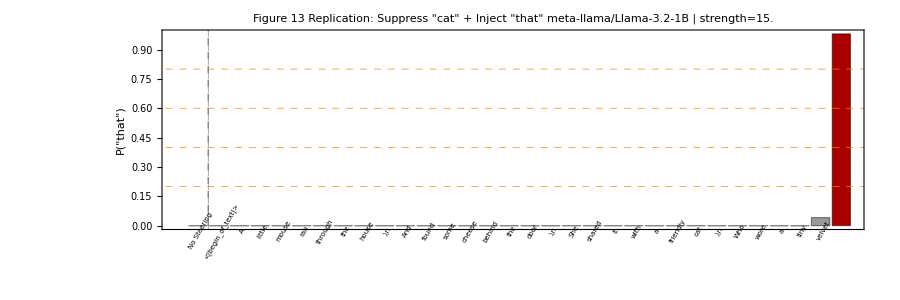

```mathematica
(* --- Bar chart (linear scale, full range) --- *)
fig13Linear =
Labeled[BarChart[styledBars[llamaAllProbs, nLlama],
ChartLabels->Placed[Style[#,7,FontFamily->"Consolas"]&/@allLabels,Below,Rotate[#,Pi/3]&],
PlotLabel -> Style["Figure 13 Replication: Suppress \"" <> data["suppress_word"] <> "\" + Inject \"" <> data["inject_word"] <> "\"\n" <> data["model"] <> " | strength=" <>  ToString[data["strength"]],12, Bold  ],
Frame -> True,FrameLabel -> {None,Style["P(\"" <> data["inject_word"] <> "\")", 11]},
GridLines->{{{1.5,Directive[Dashed,GrayLevel[0.5]]}},Table[gl,{gl,0.2,0.8,0.2}]},GridLinesStyle->Directive[Orange,Dashed],
ImageSize -> 900,AspectRatio -> 1/3,
PlotRangePadding -> {{Scaled[0.01], Scaled[0.01]}, {0, Scaled[0.05]}},
Epilog->{Dashed,Thin,GrayLevel[0.5],Line[{{1.5,0},{1.5,1}}]}],
Style["Token position",11],
Bottom]
```

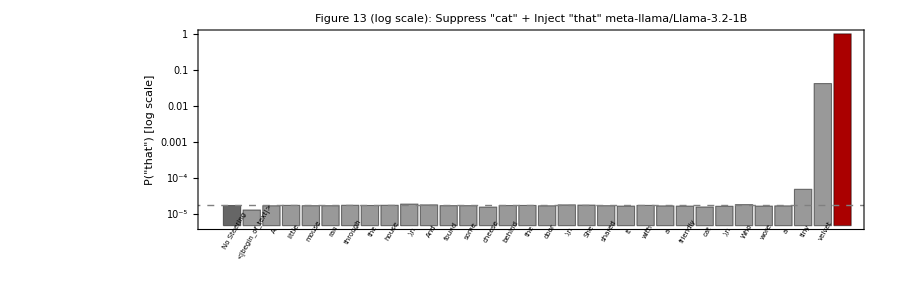

```mathematica
(* --- Bar chart (log scale) --- *)
fig13Log =
Labeled[ BarChart[styledBars[llamaAllProbs, nLlama],
ChartLabels->Placed[Style[#,7,FontFamily->"Consolas"]&/@allLabels,Below,Rotate[#,Pi/3]&],
ScalingFunctions -> "Log",
PlotLabel -> Style["Figure 13 (log scale): Suppress \"" <> data["suppress_word"] <> "\" + Inject \"" <> data["inject_word"] <>"\"\n" <> data["model"], 12, Bold ],
FrameLabel -> {None,Style["P(\"" <> data["inject_word"] <> "\") [log scale]", 11]},Frame -> True,
GridLines->{None,Table[10^-gl,{gl,0,5,1}]},GridLinesStyle->Directive[Orange,Dashed],
ImageSize -> 900,AspectRatio -> 1/3,
PlotRangePadding -> {{Scaled[0.01], Scaled[0.01]}, {0, Scaled[0.05]}},
Epilog -> {Dashed, Thin, GrayLevel[0.5],InfiniteLine[{0, Log[baseline]}, {1, 0}]}],
Style["Token position", 11],
Bottom]
```

#### Exporting the figures as PNG files

```mathematica
Export[
  FileNameJoin[{NotebookDirectory[], "figure13_linear.png"}],
  fig13Linear,
  ImageResolution -> 300
]
```

C:\Users\Eric JACOPIN\Documents\Code\Source\candle-mi\examples\figure13\figure13_linear.png

```mathematica
Export[
  FileNameJoin[{NotebookDirectory[], "figure13_log.png"}],
  fig13Log,
  ImageResolution -> 300
]
```

C:\Users\Eric JACOPIN\Documents\Code\Source\candle-mi\examples\figure13\figure13_log.png

## Gemma 2 2B with 426K CLTs

```mathematica
(* ================================================================== *)
(* PART 2: Gemma 2 2B                                                 *)
(* ================================================================== *)

gemmaData = Import[
  FileNameJoin[{NotebookDirectory[], "gemma_output.json"}],
  "RawJSON"
];

gemmaSweep = extractSweep[gemmaData];
gemmaProbs = gemmaSweep["probs"];
gemmaTokens = gemmaSweep["tokens"];
gemmaBaseline = gemmaSweep["baseline"];
gemmaLabels = cleanToken /@ gemmaTokens;

(* Prepend baseline as "No Steering" bar *)
gemmaAllProbs = Prepend[gemmaProbs, gemmaBaseline];
gemmaAllLabels = Prepend[gemmaLabels, "No Steering"];
nGemma = Length[gemmaAllProbs]
```

33

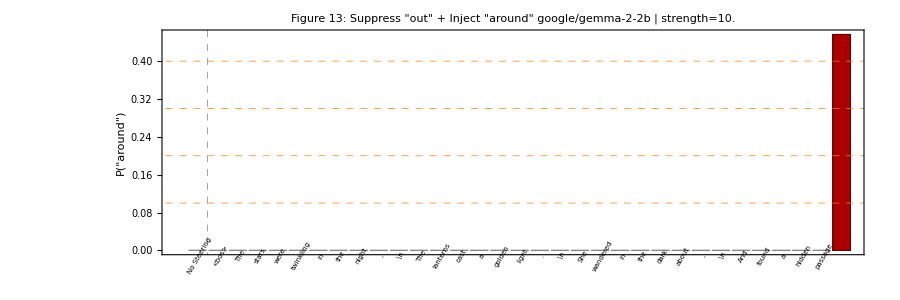

```mathematica
(* --- Gemma: linear scale --- *)
gemmaLinear =
Labeled[ BarChart[styledBars[gemmaAllProbs, nGemma],
ChartLabels -> Placed[Style[#,7, FontFamily -> "Consolas"] & /@ gemmaAllLabels,Below, Rotate[#, Pi/3] & ],PlotLabel -> Style["Figure 13: Suppress \"" <> gemmaData["suppress_word"] <> "\" + Inject \"" <> gemmaData["inject_word"] <> "\"\n" <> gemmaData["model"] <> " | strength=" <> ToString[gemmaData["strength"]],12, Bold ],Frame -> True,FrameLabel -> {None,Style["P(\"" <> gemmaData["inject_word"] <> "\")", 11]},
GridLines->{{{1.5,Directive[Dashed,GrayLevel[0.5]]}},Table[gl,{gl,0.1,0.8,0.1}]},GridLinesStyle->Directive[Orange,Dashed],
ImageSize -> 900,AspectRatio -> 1/3,PlotRangePadding -> {{Scaled[0.01], Scaled[0.01]}, {0, Scaled[0.05]}},
GridLines -> {{{1.5, Directive[Dashed, GrayLevel[0.5]]}}, None}],
Style["Token position", 11],
Bottom]
```

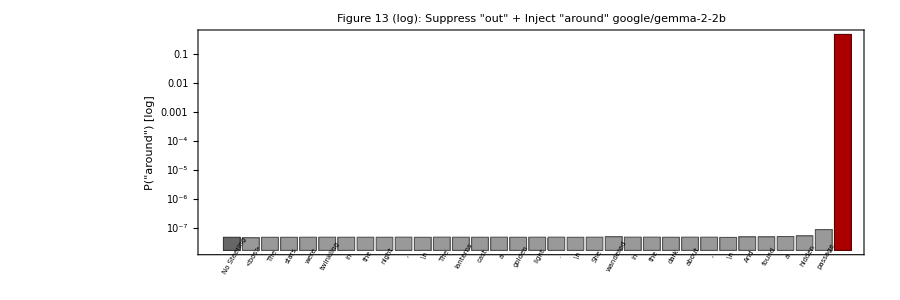

```mathematica
(* --- Gemma: log scale --- *)
gemmaLog = 
Labeled[BarChart[styledBars[gemmaAllProbs, nGemma],
ChartLabels -> Placed[Style[#, 7, FontFamily -> "Consolas"] & /@ gemmaAllLabels,Below, Rotate[#, Pi/3] &],
ScalingFunctions -> "Log",
PlotLabel -> Style["Figure 13 (log): Suppress \"" <> gemmaData["suppress_word"] <> "\" + Inject \"" <> gemmaData["inject_word"] <> "\"\n" <> gemmaData["model"],12, Bold ],
Frame -> True,FrameLabel -> {None,Style["P(\"" <> gemmaData["inject_word"] <> "\") [log]", 11]},
GridLines->{None,Table[10^-gl,{gl,0,7,1}]},GridLinesStyle->Directive[Orange,Dashed],
ImageSize -> 900,AspectRatio -> 1/3,
PlotRangePadding -> {{Scaled[0.01], Scaled[0.01]}, {0, Scaled[0.05]}},
GridLines -> {{{1.5, Directive[Dashed, GrayLevel[0.5]]}}, None}],
Style["Token position", 11],
Bottom]
```

#### Exporting the figures as PNG files

```mathematica
(* Export Gemma PNGs *)
Export[
  FileNameJoin[{NotebookDirectory[], "gemma_linear.png"}],
  gemmaLinear, ImageResolution -> 300
]
```

C:\Users\Eric JACOPIN\Documents\Code\Source\candle-mi\examples\figure13\gemma_linear.png

```mathematica
Export[
  FileNameJoin[{NotebookDirectory[], "gemma_log.png"}],
  gemmaLog, ImageResolution -> 300
]
```

C:\Users\Eric JACOPIN\Documents\Code\Source\candle-mi\examples\figure13\gemma_log.png